```mathematica
(16+13+14+17+15-13)/(18+17+16+18+15.-17)
```

0.925373

```mathematica
{a,as,b,c,cs,d,ds,e,f,fs,g,gs} ={440*2^(0/12),440*2^(1/12),440*2^(2/12),440*2^(3/12),440*2^(4/12),440*2^(5/12),440*2^(6/12),440*2^(7/12),440*2^(8/12),440*2^(9/12),440*2^(10/12),440*2^(11/12)}//N;
F[frequency_,t_]:=A*Cos[frequency 2π t]
```

```mathematica
A=1;
(*Plot[{F[c,t]+F[e,t]+F[g,t]+F[c,t]*2},{t,0,.1}];
Plot[{F[c,t]+F[e,t]+F[g,t]+F[as,t]},{t,0,.1}];
Plot[{F[c,t]+F[f,t]+F[a,t]},{t,0,.1}];*)
```

```mathematica
Play[{Sin[c 2Pi t],Sin[e 2Pi t],Sin[g 2Pi t],Sin[c*2 2Pi t]},{t,0,3}]
```

-Graphics-

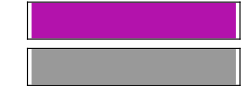

```mathematica
Sound[SoundNote["C",1,"Violin"]]
```

```mathematica
Play[Sin[443.445 2Pi t],{t,0,3}]
```

-Graphics-

```mathematica
440*2^(1/12)//N
```

466.164